# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# TFIM

```mathematica
tlist=Table[10^i,{i,-1,12,0.0010}];
tlist//Length
```

13001

```mathematica
L=6;
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
J=1;
hlist=Table[10^i,{i,-1,0.5,0.05}];
hlist=Table[10^i,{i,-8,-1,0.5}];
g=10^(-5.);
g=0.;
hlist//Length
```

15

```mathematica
allvalues={};
allvectors={};
Do[
Ha=IsingHamiltonian[hlist[[h]],g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];
,{h,Length[hlist]}];
```

```mathematica
ini=RandomChainProductState[L];
```

```mathematica
data={};
Do[
phaseTable=Exp[-I Outer[Times,allvalues[[h]],tlist]];
psitb=Compile[{{ck,_Complex,1},{phaseTable,_Complex,2}},ck*phaseTable,CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];
ck=Conjugate[allvectors[[h]]].ini;
Developer`ToPackedArray/@{allvalues[[h]],allvectors[[h]],ck,phaseTable};
t=psitb[ck,phaseTable];
final=Transpose[allvectors[[h]]].t;
entropy=ParallelMap[new,Transpose[final]];
AppendTo[data,entropy];
,{h,Length[hlist]}];
```

# Plotting

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
w=200;
tmin=First@tlist;tmax=Last@tlist;
raw=Transpose[{tlist,#}]&/@data;
sm=Transpose[{MovingAverage[tlist,w],MovingAverage[#,w]}]&/@data;
yPage=Quiet@CheckAbort[N@pageEntropy[L/2,L/2],$Failed];
ref=Join[If[NumericQ@yPage,{Directive[Black,AbsoluteThickness[3.5],AbsoluteDashing[{10,6}]],Line[{{tmin,yPage},{tmax,yPage}}]},{}],{Directive[Green,AbsoluteThickness[3.5],AbsoluteDashing[{10,6}]],Line[{{tmin,1.0},{tmax,1.0}}]}];
```

```mathematica
plot=ListLinePlot[Join[raw,sm],ScalingFunctions->{"Log10",None},PlotStyle->Join[ConstantArray[Directive[Gray,Opacity[0.02]],Length@raw],(Directive[#,AbsoluteThickness[1.6],Opacity[1]]&/@reds)],PlotRange->{{tmin,tmax},All},ImageSize->800,Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotLabel->Style[Row[{"TFIM, OBC, RPS, L = ",L,", J = ",J,", g = ",g}],25,Black],Epilog->ref,Background->White];
```

```mathematica
Export["test.png",plot,ImageSize->1000]
```

# Automatization (works)

```mathematica
(* ==========================================*)(*1. SETUP& DEFINITIONS*)(* ==========================================*)SetDirectory[NotebookDirectory[]];
(*Check if package exists,handle potential loading issues*)
If[FileExistsQ["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"],Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"],Print["Error: Package file not found. Check path."]];
(*Launch Kernels if not already running*)
If[Length[Kernels[]]<14,LaunchKernels[14]];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
(*---Helper Function:Parity Map Generation---*)
(*Encapsulated to keep the main loop clean*)
getParityMaps[L_]:=Module[{visited,evenMap,oddMap,j},visited=ConstantArray[False,2^L];
evenMap={};
oddMap={};
Do[If[!visited[[i+1]],j=revIndex[i,L];(*Assumes revIndex is in QMB_offline.wl*)visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],(*Else:Pair*)AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];];],{i,0,(2^L)-1}];
{evenMap,oddMap}];
```

```mathematica
(* ==========================================*)
(*2. PARAMETER DEFINITIONS*)
(* ==========================================*)
(*1. System Dimensions*)
Lvalues={6,8};
(*2. Time Grid*)
tlist=Table[10^i,{i,-1,12,0.010}];
(*3. Field Parameters*)
J=1;
(*g:10^-8 to 10^-1 in steps of 0.5 in exponent*)
gExponents=Range[-8,-1,1.];
(*h:Two distinct ranges as requested*)
hRanges={(*Label,List of values*){"LowField",Table[10^i,{i,-8,-1,2.}]},{"HighField",Table[10^i,{i,-1,0.5,0.5}]}};
```

```mathematica
(* ==========================================*)
(*3. AUTOMATED EXECUTION LOOP*)
(* ==========================================*)

Do[(*---------------------------------------*)(*A.LEVEL 1:DIMENSION (L)*)(*---------------------------------------*)Print[Style["\nStarting computation for L = "<>ToString[L],Bold,Blue,18]];
(*1. Fix Initial State for this Dimension*)(*This ensures all g and h sweeps for L=10 use the EXACT same psi0*)ini=RandomChainProductState[L];
(*2. Precompute Parity Maps*)
{evenMap,oddMap}=getParityMaps[L];
(*---------------------------------------*)(*B.LEVEL 2:LONGITUDINAL FIELD (g)*)(*---------------------------------------*)
Do[
gVal=10.^gExp;
Print[Style["  Running g = 10^"<>ToString[NumberForm[gExp,{2,1}]],Darker[Green],14]];
(*---------------------------------------*)(*C.LEVEL 3:TRANSVERSE FIELD (h Ranges)*)(*---------------------------------------*)
Do[
rangeName=hSet[[1]];
hList=hSet[[2]];
Print["    Processing ",rangeName," (",Length[hList]," values)..."];
(*Storage for this batch:Stores {h,EntropyList} pairs*)batchResults={};
(*Iterate over specific h values in this range*)Do[hVal=currentH;(*Renaming for clarity*)(*---1. DIAGONALIZATION---*)(*Construct Hamiltonian*)Ha=IsingHamiltonian[hVal,gVal,J,L,BoundaryConditions->"Open"];
(*Block Diagonalization*)system=BlockDiagonalize[Ha,Symmetry->"Parity"];
(*Solve Even Sector*){evenvals,evenvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
neweven=Table[ExpandBlockVector[vec,evenMap,"even",L],{vec,evenvecs}];
(*Solve Odd Sector*){oddvals,oddvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
newodd=Table[ExpandBlockVector[vec,oddMap,"odd",L],{vec,oddvecs}];
(*Recombine and Sort*)allvecs=Join[neweven,newodd];
allvals=Join[evenvals,oddvals];
sortedSystem=SortBy[Transpose[{allvals,allvecs}],First];
vals=sortedSystem[[All,1]];
vecs=sortedSystem[[All,2]];
(*---2. TIME EVOLUTION---*)(*Optimized Compiled Function for Phase*)psitb=Compile[{{ck,_Complex,1},{phases,_Complex,2}},ck*phases,CompilationTarget->"WVM",RuntimeOptions->"Speed"];
(*Compute Overlaps c_k= <E_k|psi_0>*)ck=Conjugate[vecs].ini;
(*Create Phase Table:Exp[-i E_k t]*)phaseTable=Exp[-I Outer[Times,vals,tlist]];
(*Evolve Coefficients:c_k(t)*)(*Developer`ToPackedArray improves speed significantly*)tCoeffs=psitb[Developer`ToPackedArray[ck],Developer`ToPackedArray[phaseTable]];
(*Reconstruct State: |psi(t)> =sum c_k(t)|E_k>*)(*Result'final' is Matrix[Dimension x TimeSteps]*)finalState=Transpose[vecs].tCoeffs;
(*---3. ENTROPY CALCULATION---*)(*Parallel Map over Time Steps*)(*Note:Assumes'new' is the entropy function from your.wl package*)(*We define'new' to all kernels just in case*)DistributeDefinitions[new];
entropySeries=ParallelMap[new,Transpose[finalState]];
(*Store Result*)AppendTo[batchResults,{hVal,entropySeries}];
(*CLEANUP MEMORY inside inner loop to prevent buildup*)Clear[Ha,system,evenvals,oddvals,neweven,newodd,allvecs,allvals,vals,vecs,phaseTable,finalState];,{currentH,hList}];(*End h Loop*)(*---------------------------------------*)(*SAVE DATA IMMEDIATELY*)(*---------------------------------------*)(*Filename:Entropy_L6_g-5.0_LowField.mx*)exportName="Entropy_L"<>ToString[L]<>"_g"<>ToString[NumberForm[gExp,{2,1}]]<>"_"<>rangeName<>".mx";
(*Export as an Association for easy retrieval later*)Export[exportName,<|"L"->L,"J"->J,"g"->gVal,"h_range_name"->rangeName,"tlist"->tlist,"h_values"->hList,"initial_state"->ini,"data"->batchResults (*List of {h,entropy_time_series}*)|>];
Print["    Saved: "<>exportName];
Clear[batchResults]; (*Free batch memory*),{hSet,hRanges}]; (*End h_ranges Loop*),{gExp,gExponents}]; (*End g Loop*),{L,Lvalues}]; (*End L Loop*)

Print["\nAll computations completed successfully."];
```

# Melting time

```mathematica
(* ==========================================*)(*PART 3:TIME SCALE EXTRACTION (from.mx)*)(* ==========================================*)SetDirectory[NotebookDirectory[]];
(*1. ANALYSIS HELPER*)
ClearAll[ExtractCrossingTime];
ExtractCrossingTime[timeList_,entropy_,window_:200,threshold_:0.693147]:=Module[{smoothS,smoothT,crossIdx,t1,t2,s1,s2,sClean},(*Cleaning:Take Re[] and Flatten to match Plotting logic*)sClean=Re[Flatten[entropy]];
If[Length[timeList]!=Length[sClean],Return[Indeterminate]];
(*Smooth data*)smoothS=MovingAverage[sClean,window];
smoothT=MovingAverage[timeList,window];
(*Find crossing*)crossIdx=FirstPosition[smoothS,_?(#>=threshold&)];
If[MissingQ[crossIdx],Return[Indeterminate]];
crossIdx=crossIdx[[1]];
If[crossIdx==1,Return[smoothT[[1]]]];
(*Interpolate*)t1=smoothT[[crossIdx-1]];t2=smoothT[[crossIdx]];
s1=smoothS[[crossIdx-1]];s2=smoothS[[crossIdx]];
t1+(t2-t1)*(threshold-s1)/(s2-s1)];
```

```mathematica
(*2. PARAMETERS*)
L=6;
crossingThreshold=Log[2];
gExponents=Range[-8,-1,0.5]; (*Matches your file names*)
hRanges={"LowField","HighField"};
```

```mathematica
(*3. MAIN LOOP*)
Do[(*Construct g-string matches filename format:"g-2.0"*)gStr=StringDelete[ToString[NumberForm[gExp,{2,1}]]," "];
Do[type=rangeName;
crossingTimes={};
(*A.Construct Path to.mx file*)fileName="Entropy_L"<>ToString[L]<>"_g"<>gStr<>"_"<>type<>".mx";
fullPath=FileNameJoin[{NotebookDirectory[],"Data","L"<>ToString[L],fileName}];
Print["Reading: ",fileName];
(*B.Import& Process*)If[FileExistsQ[fullPath],(*Import the full association*)dataAssoc=Import[fullPath];
tlist=Flatten[dataAssoc["tlist"]];(*Extract time grid*)allCurves=dataAssoc["data"];(*Structure:{{h,s_list},...}*)(*Iterate over all h values in this file*)Do[hVal=curveData[[1]];
sSeries=curveData[[2]];
(*Extract Time*)tm=ExtractCrossingTime[tlist,sSeries,200,crossingThreshold];
If[NumericQ[tm],AppendTo[crossingTimes,{hVal,tm}]];,{curveData,allCurves}];
(*C.Export Results (Save to Data/L6 folder)*)If[Length[crossingTimes]>0,outputBase="TimeScale_L"<>ToString[L]<>"_g"<>gStr<>"_"<>type;
outputDir=DirectoryName[fullPath];(*Save next to.mx file*)(*Save.dat*)Export[FileNameJoin[{outputDir,outputBase<>".dat"}],crossingTimes,"Table"];
(*Plot& Save.png*)plot=ListLogLogPlot[crossingTimes,Frame->True,PlotStyle->{Red,PointSize[0.02]},Joined->True,FrameLabel->{"Field Strength (h)","Crossing Time (\!\(\*SubscriptBox[\(T\), \(M\)]\))"},PlotLabel->"L="<>ToString[L]<>", g=10^"<>gStr<>" ("<>type<>")",GridLines->Automatic,PlotTheme->"Scientific"];
Export[FileNameJoin[{outputDir,outputBase<>".png"}],plot];
Print["   -> Exported: ",outputBase];];,Print["   -> File Not Found! (Skipping)"];];,{rangeName,hRanges}];,{gExp,gExponents}];
```

# Automatization 2

```mathematica
(* ==========================================*)(*PART 1:AUTOMATED SIMULATION ENGINE*)(* ==========================================*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Survival\\QMB_offline_new.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
(*2. SETUP*)
LaunchKernels[14];
```

```mathematica
(*Helper:Parity Maps*)
getParityMaps[L_]:=Module[{visited,evenMap,oddMap,j},visited=ConstantArray[False,2^L];
evenMap={};oddMap={};
Do[If[!visited[[i+1]],j=revIndex[i,L];
visited[[i+1]]=True;visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];AppendTo[oddMap,{i,j}];];],{i,0,(2^L)-1}];
{evenMap,oddMap}];
```

```mathematica
(*4. PARAMETERS*)
Lvalues={6};          (*System Sizes*)
J=1;                             (*Coupling*)
gExponents=Range[-8,-1,0.5];   (*g=10^-8 to 10^-1*)
tlist=Table[10^i,{i,-1,12,0.001}]; (*Time grid*)
(*h Ranges:Split into Low and High for easier analysis*)
hRanges={{"LowField",Table[10^i,{i,-8,-1,0.1}]},{"HighField",Table[10^i,{i,-1,0.5,0.05}]}};
```

```mathematica
(*4. EXECUTION LOOP*)
Do[(*---Create Directory for Data---*)currentDataDir=FileNameJoin[{NotebookDirectory[],"Data","L"<>ToString[L]}];
If[!DirectoryQ[currentDataDir],CreateDirectory[currentDataDir,CreateIntermediateDirectories->True]];
Print[Style["\nStarting computation for L = "<>ToString[L],Bold,Blue,18]];
ini=RandomChainProductState[L];
{evenMap,oddMap}=getParityMaps[L];
Do[gVal=10.^gExp;
Print[Style["  Running g = 10^"<>ToString[NumberForm[gExp,{2,1}]],Darker[Green],14]];
Do[rangeName=hSet[[1]];hList=hSet[[2]];
Print["    Processing ",rangeName," (",Length[hList]," values)..."];
batchResults={};
Do[hVal=currentH;
(*Diagonalization*)Ha=IsingHamiltonian[hVal,gVal,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenvals,evenvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
neweven=Table[ExpandBlockVector[vec,evenMap,"even",L],{vec,evenvecs}];
{oddvals,oddvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
newodd=Table[ExpandBlockVector[vec,oddMap,"odd",L],{vec,oddvecs}];
allvecs=Join[neweven,newodd];allvals=Join[evenvals,oddvals];
sortedSystem=SortBy[Transpose[{allvals,allvecs}],First];
vals=sortedSystem[[All,1]];
vecs=sortedSystem[[All,2]];
(*Time Evolution*)
psitb=Compile[{{ck,_Complex,1},{phases,_Complex,2}},ck*phases,CompilationTarget->"WVM",RuntimeOptions->"Speed"];
ck=Conjugate[vecs].ini;
phaseTable=Exp[-I Outer[Times,vals,tlist]];
tCoeffs=psitb[Developer`ToPackedArray[ck],Developer`ToPackedArray[phaseTable]];
finalState=Transpose[vecs].tCoeffs;
(*Entropy*)
DistributeDefinitions[newb];
entropySeries=ParallelMap[newb,Transpose[finalState]];
AppendTo[batchResults,{hVal,entropySeries}];
Clear[Ha,system,evenvals,oddvals,neweven,newodd,allvecs,allvals,vals,vecs,phaseTable,finalState];,{currentH,hList}];
(*SAVE DATA to subfolder*)fileNameOnly="Entropy_L"<>ToString[L]<>"_g"<>ToString[NumberForm[gExp,{2,1}]]<>"_"<>rangeName<>".mx";
exportPath=FileNameJoin[{currentDataDir,fileNameOnly}];
Export[exportPath,<|"L"->L,"J"->J,"g"->gVal,"h_range_name"->rangeName,"tlist"->tlist,"h_values"->hList,"initial_state"->ini,"data"->batchResults|>];
Print["    Saved: "<>fileNameOnly];
Clear[batchResults];,{hSet,hRanges}];,{gExp,gExponents}];,{L,Lvalues}];
```

# Automated plotting

```mathematica
(* ==========================================*)(*ROBUST PLOTTING ENGINE (Fixes Missing Lines)*)(* ==========================================*)SetDirectory[NotebookDirectory[]];
(*1. HELPER DEFINITIONS*)
If[!ValueQ[pageEntropy],pageEntropy[La_,Lb_]:=(La*Log[2]-0.5)];
myGradient=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
(*2. PLOTTING FUNCTION*)
processAndPlot[fullPath_]:=Module[{dataAssoc,L,g,hRangeName,tlist,hValues,rawData,w,tSmoothed,plotData,minLogH,maxLogH,colorList,legend,yPage,plotTitle,outputDir,pngName,finalPath,finalPlot,tMin,tMax,sClean,entropyData},(*---A.Import---*)Print["-------------------------------------------------"];
Print["Reading: ",FileBaseName[fullPath]];
dataAssoc=Import[fullPath];
L=dataAssoc["L"];
g=dataAssoc["g"];
hRangeName=dataAssoc["h_range_name"];
tlist=Flatten[dataAssoc["tlist"]];(*Force Flat*)hValues=dataAssoc["h_values"];
rawData=dataAssoc["data"];
(*Define Directory:SAME as Data File*)outputDir=DirectoryName[fullPath];
(*---B.Data Preparation (Crucial Fixes)---*)w=100;(*Window size*)tSmoothed=MovingAverage[tlist,w];
tMin=Min[tlist];
tMax=Max[tlist];
(*Construct curves safely*)plotData=Table[entropyData=entry[[2]];
(*SAFETY 1:Flatten and take Real part to ensure simple numbers*)sClean=MovingAverage[Re[Flatten[entropyData]],w];
(*Check lengths match before pairing*)If[Length[tSmoothed]!=Length[sClean],Print["Error: Length mismatch for h=",entry[[1]]];{},Transpose[{tSmoothed,sClean}]],{entry,rawData}];
(*---C.Styling---*)minLogH=Min[Log10[hValues]];
maxLogH=Max[Log10[hValues]];
If[minLogH==maxLogH,colorList={Blue};
legend=Placed["h = "<>ToString[hValues[[1]]],Right];,colorList=Table[myGradient[Rescale[Log10[h],{minLogH,maxLogH}]],{h,hValues}];
legend=BarLegend[{myGradient,{minLogH,maxLogH}},"Ticks"->Range[Ceiling[minLogH],Floor[maxLogH]],"TickLabels"->(Superscript[10,#]&/@Range[Ceiling[minLogH],Floor[maxLogH]]),LegendLabel->Style["Field (h)",Black,14],LegendMarkerSize->300];];
(*---D.References---*)yPage=N[pageEntropy[L/2,L/2]];
(*---E.Generate Plot---*)plotTitle=Row[{"L=",L,", g=",NumberForm[g,{3,5}]," (",hRangeName,")"}];
finalPlot=ListLogLinearPlot[plotData,PlotStyle->colorList,(*Fixed Range:0 to Page Value+small buffer*)PlotRange->{{tMin,tMax},{0,yPage*1.2}},Frame->True,FrameStyle->Directive[Black,18],FrameLabel->{Style["Time (t)",22],Style["Entropy \!\(S(t)\)",22]},PlotLabel->Style[plotTitle,20,Black],ImageSize->800,Joined->True,(*Reference Lines*)Epilog->{(*Page Entropy (Black Dashed)*)Directive[Black,Dashed,AbsoluteThickness[2]],Line[{{tMin,yPage},{tMax,yPage}}],(*S=1.0 (Green Dashed)*)Directive[Green,Dashed,AbsoluteThickness[2]],Line[{{tMin,1.0},{tMax,1.0}}]},PlotLegends->Placed[legend,Right]];
(*---F.Export---*)(*Fix:Ensure extension is.png*)pngName=FileBaseName[fullPath]<>".png";
finalPath=FileNameJoin[{outputDir,pngName}];
Export[finalPath,finalPlot];
Print["   -> Saved Plot: ",finalPath];];
```

```mathematica
(*3. EXECUTE BATCH*)files=FileNames["Entropy_*.mx",{FileNameJoin[{NotebookDirectory[],"Data"}]},Infinity];
If[Length[files]==0,Print["No data files found! Run Part 1."],Do[processAndPlot[f],{f,files}]];
```

# Melting time

```mathematica
(* ::Section::*)
(*3) Processing:extract crossing times->TimeScale_*.dat (one per Entropy_*.mx)*)
ClearAll[ExtractCrossingTime];
ExtractCrossingTime[timeList_,entropy_,window_:200,threshold_:N@Log[2]]:=Module[{sClean,smoothS,smoothT,crossPos,k,t1,t2,s1,s2},sClean=Re@Flatten@entropy;
If[Length[timeList]=!=Length[sClean],Return[Indeterminate]];
smoothS=MovingAverage[sClean,window];
smoothT=MovingAverage[timeList,window];
crossPos=FirstPosition[smoothS,_?(#>=threshold&)];
If[MissingQ[crossPos],Return[Indeterminate]];
k=crossPos[[1]];
If[k==1,Return[smoothT[[1]]]];
t1=smoothT[[k-1]];t2=smoothT[[k]];
s1=smoothS[[k-1]];s2=smoothS[[k]];
t1+(t2-t1) (threshold-s1)/(s2-s1)];
```

```mathematica
crossingWindow=200;
crossingThreshold=N@Log[2];
processCrossingTimes[fullPath_]:=Module[{dataAssoc,tlistLocal,curves,crossingTimes,outBase,outPath},Print["Processing crossings: ",FileBaseName[fullPath]];
dataAssoc=Import[fullPath];
tlistLocal=Flatten[dataAssoc["tlist"]];
curves=dataAssoc["data"];
crossingTimes=Reap[Do[With[{hVal=curve[[1]],sSeries=curve[[2]]},With[{tm=ExtractCrossingTime[tlistLocal,sSeries,crossingWindow,crossingThreshold]},If[NumericQ[tm],Sow[{hVal,tm}]]]],{curve,curves}]][[2]];
crossingTimes=If[crossingTimes==={},{},First[crossingTimes]];
If[crossingTimes==={},Return[]];
outBase=StringReplace[FileBaseName[fullPath],StartOfString~~"Entropy"->"TimeScale"];
outPath=FileNameJoin[{DirectoryName[fullPath],outBase<>".dat"}];
Export[outPath,crossingTimes,"Table"];
Print["   -> Saved: ",outPath];];

If[entropyMX==={},Print["No Entropy_*.mx files found."],Scan[processCrossingTimes,entropyMX]];
```

```mathematica
(* ::Section::*)(*4) Plotting:TimeScale(h) from TimeScale_*.dat (minimal first pass)*)
fixedPlotRanges=<|"LowField"->{10^-8,10^-1},"HighField"->{10^-1,10^0.5}|>;

(*---metadata parser from filename---*)
timeScaleMeta[datPath_]:=Module[{base,rangeName,gExpStr,gExp,gVal,Lstr},base=FileBaseName[datPath];
rangeName=Last@StringSplit[base,"_"];
gExpStr=First@StringCases[base,"g"~~x:Shortest[__]~~"_":>x];
gExp=ToExpression[gExpStr];
gVal=10.^gExp;
Lstr=First@StringCases[base,"L"~~x:DigitCharacter..:>x];
<|"Base"->base,"RangeName"->rangeName,"gExpStr"->gExpStr,"gExp"->gExp,"gVal"->gVal,"Lstr"->Lstr|>];

(*---Plot 1:raw data only (minimal log-log)---*)
rawTimeScalePlot[data_,xRange_,plotTitle_]:=ListLogLogPlot[data,PlotRange->{xRange,Automatic},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotStyle->Black,PlotMarkers->{Style["○",18],14},Joined->False,Frame->True,FrameLabel->{"Field Strength (h)","Crossing Time (T_M)"},PlotLabel->plotTitle,ImageSize->1000];

(*---Plot 2:vertical g-line only (independent plot,then combined with Show)---*)
gLinePlot[gVal_,gExpStr_,xRange_,yRange_]:=Module[{xLine,gLabel},xLine=Clip[gVal,xRange];(*ensures a visible line even if g is off-window*)gLabel=Row[{"g = ",Superscript["10",gExpStr]}];
ListLogLogPlot[{{xLine,yRange[[1]]},{xLine,yRange[[2]]}},PlotRange->{xRange,yRange},PlotStyle->Directive[Blue,Dashed,AbsoluteThickness[3]],Joined->True,Axes->False,Frame->False,GridLines->None,PlotMarkers->None,Epilog->{Text[Style[gLabel,Blue,18,Background->White],Scaled[{0.70,0.60}]   (*always visible;independent of data coordinates*)]}]];
```

```mathematica
(*START TO MODIFY HERE*)
```

```mathematica
datPath=First@FileNames["TimeScale_*_LowField.dat",{FileNameJoin[{projectDir,"Data"}]},Infinity];
data=Import[datPath,"Table"];
data=Select[data,NumericQ[#[[1]]]&&NumericQ[#[[2]]]&&#[[1]]>0&&#[[2]]>0&];
base=FileBaseName[datPath];
```

```mathematica
datPath=First@FileNames["TimeScale_*_LowField.dat",{FileNameJoin[{projectDir,"Data"}]},Infinity];
data=Import[datPath,"Table"];
data=Select[data,NumericQ[#[[1]]]&&NumericQ[#[[2]]]&&#[[1]]>0&&#[[2]]>0&];
```

```mathematica
gVal=10.^ToExpression[gExpStr];
```

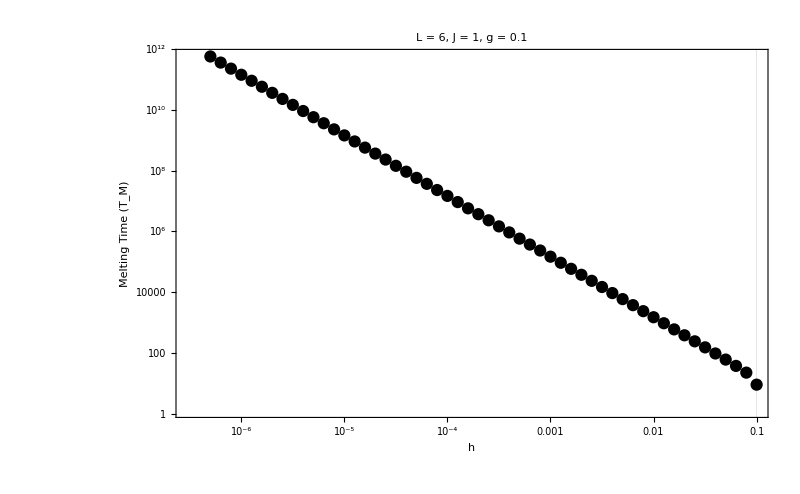

```mathematica
plot1=ListLogLogPlot[data,PlotRange->All,GridLines->{{gVal},None},GridLinesStyle->{Directive[Red,Thick],None},PlotTheme->"Detailed",PlotRange->{xRange,All},Frame->True,FrameStyle->Directive[Black,24],ImageSize->800,FrameLabel->{Style["h",28],Style["Melting Time (\!\(\*SubscriptBox[\(T\), \(M\)]\))",28]},PlotLabel->Style["L = "<>ToString[Lvalues[[1]]]<>", J = 1, g = "<>ToString[gVal],25,Black],PlotStyle->Directive[Black]]
```